# projector

## smooth projector

## Exp[κ(x-1)/x], which is smooth for x ∈ (0,∞)

```mathematica
Simplify[Exp[κ(x-1)/x]-(Exp[κ]Exp[-κ/x])]
```

0

## If[x≤ 0,0,Exp[κ(x-1)/x]], which is smooth for x ∈ (-∞,∞)

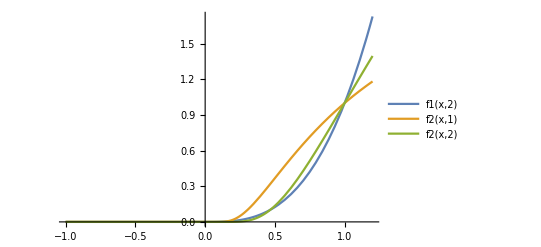

```mathematica
f1[x_,n_]:=If[x≤ 0,0,(x^(n+1))]
f2[x_,κ_]:=If[x≤ 0,0,Exp[κ(x-1)/x]]
Plot[{f1[x,2],f2[x,1],f2[x,2]},{x,-1,1.2}, PlotLegends->"Expressions"]
```

## visualize Exp[κ(x-1)/x]and its derivative for different κ

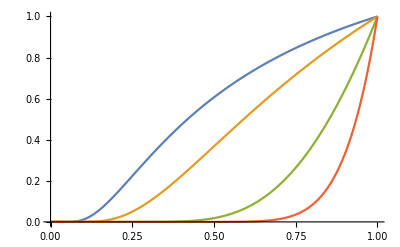

0

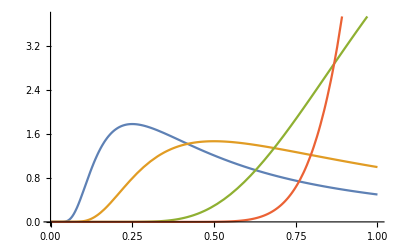

```mathematica
Plot[{
Exp[κ(x-1)/x]/.{κ-> 0.5},
Exp[κ(x-1)/x]/.{κ-> 1},
Exp[κ(x-1)/x]/.{κ-> 4},
Exp[κ(x-1)/x]/.{κ-> 10}
},{x,0,1}]
(*derivative*)
(ⅇ^(((-1+x) κ)/x) κ)/x^2-Evaluate[D[Exp[κ(x-1)/x],x]]//Simplify
Plot[{
(ⅇ^(((-1+x) κ)/x) κ)/x^2/.{κ-> 0.5},
(ⅇ^(((-1+x) κ)/x) κ)/x^2/.{κ-> 1},
(ⅇ^(((-1+x) κ)/x) κ)/x^2/.{κ-> 4},
(ⅇ^(((-1+x) κ)/x) κ)/x^2/.{κ-> 10}
},{x,0,1}]
```

## smooth update law Projector(μ,ê):=If[(ê.ê-ebar^2)≤ 0,μ,Projector2[μ,ê,{ebar,êbar,μbar,κ}]]

The projector operator is smooth, but because it is defined with an “if” condition, it makes the differentiation of the projector complicated and it makes the symbolic calculations really slow later on. That is the main reason for the next auxiliary definitions

```mathematica
EstimatorProj2[μ_,ehat_,{ebar_,ehatbar_,μbar_,κ_}]:=μ-(Exp[κ(#-1)/#]&[(ehat.ehat-ebar^2)/(ehatbar^2-ebar^2)])1/2((ehat/ebar).μ+√(((ehat/ebar).μ)^2+μbar^2))ehat/ebar
(*derivative with respect to first argument*)
d1EstimatorProj2[{μ1_,μ2_,μ3_},{ehat1_,ehat2_,ehat3_},{ebar_,ehatbar_,μbar_,κ_}]=Simplify[
Evaluate[
D[EstimatorProj2[{μ1,μ2,μ3},{ehat1,ehat2,ehat3},{ebar,ehatbar,μbar,κ}],{{μ1,μ2,μ3}}]
]
];
(*derivative with respect to second argument*)
d2EstimatorProj2[{μ1_,μ2_,μ3_},{ehat1_,ehat2_,ehat3_},{ebar_,ehatbar_,μbar_,κ_}]=Simplify[
Evaluate[D[EstimatorProj2[{μ1,μ2,μ3},{ehat1,ehat2,ehat3},{ebar,ehatbar,μbar,κ}],{{ehat1,ehat2,ehat3}}]
]
];
```

### strange behaviour by mathematica!

```mathematica
If[x≤0,{μ1,μ2},2{μ1,μ2}]-{μ1,μ2}
{a,b}.If[x≤0,{μ1,μ2},2{μ1,μ2}]
```

{-μ1+If[x≤0,{μ1,μ2},2 {μ1,μ2}],-μ2+If[x≤0,{μ1,μ2},2 {μ1,μ2}]}

{a,b}.If[x≤0,{μ1,μ2},2 {μ1,μ2}]

```mathematica
MapThread[If[x≤0,#1,#2]&,{{μ1,μ2},2{μ1,μ2}},1]
MapThread[If[x≤0,#1,#2]&,{{μ1,μ2},2{μ1,μ2}},1]-{μ1,μ2}
```

{If[x≤0,μ1,2 μ1],If[x≤0,μ2,2 μ2]}

{-μ1+If[x≤0,μ1,2 μ1],-μ2+If[x≤0,μ2,2 μ2]}

### definition of Projector

```mathematica
(*EstimatorProj[μ_,ehat_,{ebar_,ehatbar_,μbar_,κ_}]:=If[ehat.ehat-ebar^2≤ 0,μ,EstimatorProj2[μ,ehat,{ebar,ehatbar,μbar,κ}]]*)
EstimatorProj[μ_,ehat_,{ebar_,ehatbar_,μbar_,κ_}]:=MapThread[If[ehat.ehat-ebar^2≤ 0,#1,#2]&,{μ,EstimatorProj2[μ,ehat,{ebar,ehatbar,μbar,κ}]},1]
(*test*)
EstimatorProj[RandomReal[{-2,2},3],RandomReal[{-2,2},3],{1,2,1,1}]
```

{-0.821217,-1.4604,1.62444}

### derivatives of Projector (w.r.t to 1st and 2nd arguments) d1Proj(μ,ê)=(∂Proj(μ,ê))/(∂μ) d2Proj(μ,ê)=(∂Proj(μ,ê))/(∂ê)

```mathematica
(*d1EstimatorProj[μ_,ehat_,{ebar_,ehatbar_,μbar_,κ_}]:=If[ehat.ehat-ebar^2≤ 0,IdentityMatrix[Length[μ]],d1EstimatorProj2[μ,ehat,{ebar,ehatbar,μbar,κ}]]
d2EstimatorProj[μ_,ehat_,{ebar_,ehatbar_,μbar_,κ_}]:=If[ehat.ehat-ebar^2≤ 0,ConstantArray[0,{Length[μ],Length[μ]}],d2EstimatorProj2[μ,ehat,{ebar,ehatbar,μbar,κ}]]*)
d1EstimatorProj[μ_,ehat_,{ebar_,ehatbar_,μbar_,κ_}]:=MapThread[If[ehat.ehat-ebar^2≤ 0,#1,#2]&,{IdentityMatrix[Length[μ]],d1EstimatorProj2[μ,ehat,{ebar,ehatbar,μbar,κ}]},1]
d2EstimatorProj[μ_,ehat_,{ebar_,ehatbar_,μbar_,κ_}]:=MapThread[If[ehat.ehat-ebar^2≤ 0,#1,#2]&,{ConstantArray[0,{Length[μ],Length[μ]}],d2EstimatorProj2[μ,ehat,{ebar,ehatbar,μbar,κ}]},1]
(*test*)
d1EstimatorProj[RandomReal[{-2,2},3],RandomReal[{-2,2},3],{1,2,1,1}]
d2EstimatorProj[RandomReal[{-2,2},3],RandomReal[{-2,2},3],{1,2,1,1}]
```

{{0.382089,-0.905016,-0.450948},{-0.905016,-0.325521,-0.660476},{-0.450948,-0.660476,0.6709}}

{{-0.0681815,0.0359066,-0.059351},{0.0435636,-0.145084,0.154734},{-0.0470987,0.101209,-0.218763}}

### property that involves inner product: (e-ê).(Proj(μ,ê) - μ) ≥ 0 for all e ∈ Ball^n(ebar) and ê ∈ Ball^n(êbar) and for any μ∈R^n

```mathematica
Plot3D[
({b1,b2}-{b1d,b2d}).(EstimatorProj[{μ1,μ2},{b1d,b2d},{1,2,1,1}]-{μ1,μ2})/.Thread[{μ1,μ2}-> {0.1,0.1}]/.Thread[{b1d,b2d}-> {1.9,0}],
{b1,-1,1},
{b2,-1,1},
PlotRange->{0,5},
RegionFunction->Function[{x,y},x^2+y^2≤ (1)^2]
]
```

-Graphics3D-

### Stream plot

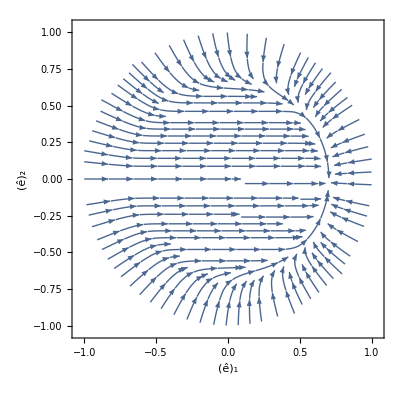

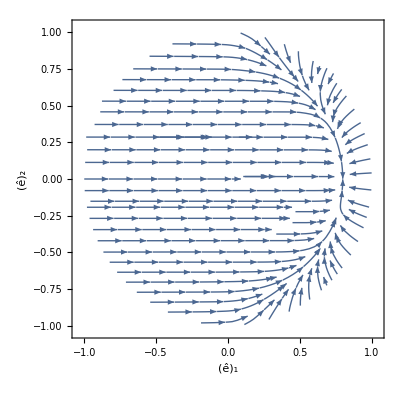

```mathematica
StreamPlot[
EstimatorProj[{1,0},{b1d,b2d},{#/2,#,10,1}],
{b1d,-#,#},
{b2d,-#,#},
StreamPoints->80,
RegionFunction->Function[{x,y},x^2+y^2≤(#)^2],
FrameLabel->{
Text[Style[ToExpression["\\hat{e}_{1}",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\hat{e}_{2}",TeXForm,HoldForm]]]
}
]&[1]
StreamPlot[
EstimatorProj[{1,0},{b1d,b2d},{#/2,#,0.1,1}],
{b1d,-#,#},
{b2d,-#,#},
StreamPoints->80,
RegionFunction->Function[{x,y},x^2+y^2≤(#)^2],
FrameLabel->{
Text[Style[ToExpression["\\hat{e}_{1}",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\hat{e}_{2}",TeXForm,HoldForm]]]
}
]&[1]
```

## n^th differentiable projector (user chooses n)

The projector operator is “sufficiently smooth”, but because it is defined with an “if” condition, it makes the differentiation of the projector complicated and it makes the symbolic calculations really slow later on. That is the main reason for the next auxiliary definitions

## smooth update law Projector(μ,bhat)=If[(bhat.bhat-bbar^2)≤ 0,μ,Projector2[μ,bhat,{θ0,ϵ,δ,n}]] bhat = estimate of disturbance b θ0 = bound on \|b\|; ϵ (\| bhat \| < θ0 + ϵ); δ (>0) n (who many derivatives do we need)

The projector operator is smooth, but because it is defined with an “if” condition, it makes the differentiation of the projector complicated and it makes the symbolic calculations really slow later on. That is the main reason for the next auxiliary definitions

### auxiliary definitions, before Projector is defined

```mathematica
EstimatorProj2[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=bdot-((b.b-θ0^2)^(n+1))/((ϵ^2+2ϵ θ0)^(n+1))(1/2 b.bdot+√((1/2 b.bdot)^2+δ^2))/(4 θ0^2)b
d1EstimatorProj2[{bdot1_,bdot2_,bdot3_},{b1_,b2_,b3_},{θ0_,ϵ_,δ_,n_}]=Simplify[
Evaluate[
D[EstimatorProj2[{bdot1,bdot2,bdot3},{b1,b2,b3},{θ0,ϵ,δ,n}],{{bdot1,bdot2,bdot3}}]
]
];
d2EstimatorProj2[{bdot1_,bdot2_,bdot3_},{b1_,b2_,b3_},{θ0_,ϵ_,δ_,n_}]=Simplify[
Evaluate[D[EstimatorProj2[{bdot1,bdot2,bdot3},{b1,b2,b3},{θ0,ϵ,δ,n}],{{b1,b2,b3}}]
]
];
```

### definition of Proj

```mathematica
EstimatorProj[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=If[(b.b-θ0^2)≤ 0,bdot,EstimatorProj2[bdot,b,{θ0,ϵ,δ,n}]]
```

### necessary derivatives

```mathematica
d1EstimatorProj[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=If[(b.b-θ0^2)≤ 0,bdot,d1EstimatorProj2[bdot,b,{θ0,ϵ,δ,n}]]
d2EstimatorProj[bdot_,b_,{θ0_,ϵ_,δ_,n_}]:=If[(b.b-θ0^2)≤ 0,bdot,d2EstimatorProj2[bdot,b,{θ0,ϵ,δ,n}]]
(*test*)
d1EstimatorProj[RandomReal[{-2,2},3],RandomReal[{-2,2},3],{1,1,1,3}]
d2EstimatorProj[RandomReal[{-2,2},3],RandomReal[{-2,2},3],{1,1,1,3}]
```

{{0.408579,0.0897371,-0.166875},{0.0897371,0.986384,0.0253201},{-0.166875,0.0253201,0.952915}}

{{-0.199749,-0.226129,-0.085731},{-0.166874,-0.263923,-0.0868098},{-0.053932,-0.0740023,-0.0630047}}

### n^th smoothness property

```mathematica
COMMENT=False
```

False

#### test n=1

```mathematica
(*derivative at boundary*)
If[!COMMENT,
Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},1}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 1}
]
If[!COMMENT,
Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},2}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 1}
]
```

{{0,0},{0,0}}

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

{{{Indeterminate,0},{0,0}},{{0,0},{0,0}}}

#### test n=2

```mathematica
(*derivative at boundary*)
If[!COMMENT,
Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},1}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 2}
]
If[!COMMENT,
Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},2}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 2}
]
(*it takes a bit of time, so i have suppressed this: but eventually it says indeterminate*)
Simplify[
D[EstimatorProj2[{b1dot,b2dot},{b1,b2},{θ0,ϵ,δ,n}],{{b1,b2},3}]/.Thread[{b1,b2}-> θ0{1,0}]
]/.{n-> 2}
```

{{0,0},{0,0}}

{{{0,0},{0,0}},{{0,0},{0,0}}}

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

{{{{Indeterminate,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}}

### property that involves inner product: (b-bhat).(Proj(μ, bhat) - μ) ≥ 0 for all d ∈ Ball^n(bbar) and bhat ∈ Ball^n(bhatbar) and for any μ∈R^n inner product > 0 provided that real b lies inside the Ball(0.5)

```mathematica
Plot3D[
({b1,b2}-{b1d,b2d}).EstimatorProj[{μ1,μ2},{b1d,b2d},{0.5,0.5,8,3}]-({b1,b2}-{b1d,b2d}).{μ1,μ2}/.Thread[{μ1,μ2}-> {0.1,0.1}]/.Thread[{b1d,b2d}-> {0.9,0}],
{b1,-1,1},
{b2,-1,1},
PlotRange->{0,5},
RegionFunction->Function[{x,y},x^2+y^2≤ (0.5)^2]
]
```

-Graphics3D-

### Stream plot is doing something funny, where there is a stream line exiting the ball, but it shouldn’t

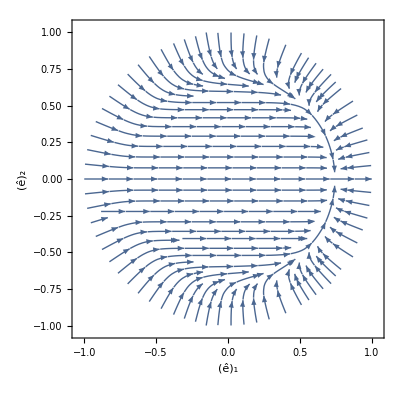

```mathematica
StreamPlot[
EstimatorProj[{0.1,0},{b1d,b2d},{#/2,#/2,5,3}],
{b1d,-#,#},
{b2d,-#,#},
StreamPoints->80,
RegionFunction->Function[{x,y},x^2+y^2≤(#)^2],
FrameLabel->{
Text[Style[ToExpression["\\hat{e}_{1}",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\hat{e}_{2}",TeXForm,HoldForm]]]
}
]&[1]
```

### stream line does not exit the ball

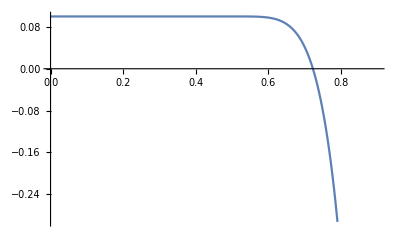

```mathematica
Plot[EstimatorProj[{0.1,0},{b1d,0},{1/2,1/2,8,3}][[1]],{b1d,0,0.9}]
```

### dirty fix (this is just to create a nice picture)

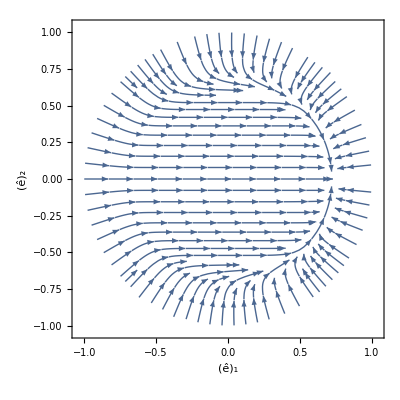

Export::nodir: Directory /Users/pedropereira/Dropbox/KTH Pessoal/written articles/2018/2018 cortes/2018r_aerial-slung-load/figures/ does not exist.

Export::noopen: Cannot open /Users/pedropereira/Dropbox/KTH Pessoal/written articles/2018/2018 cortes/2018r_aerial-slung-load/./figures/estimator_vector_field.pdf.

```mathematica
StreamPlot[
EstimatorProj[{0.1,0},{b1d,b2d},{#/2,#/2,8,3}],
{b1d,-#,#},
{b2d,-#,#},
StreamPoints->80,
RegionFunction->Function[{x,y},x^2+y^2≤(#)^2&&!(x≥0.73 &&Abs[y]<0.001)],
FrameLabel->{
Text[Style[ToExpression["\\hat{e}_{1}",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\hat{e}_{2}",TeXForm,HoldForm]]]
}
]&[1]
(*Export[NotebookDirectory[]<>"./figures/estimator_vector_field.pdf",%];*)
```